```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=35;R=2;a=0.05;μ=8/9 Subscript[m, N];
rmax=3.0;dr=0.01;
rlist=Range[0,rmax,dr];
n=Length[rlist]
```

301

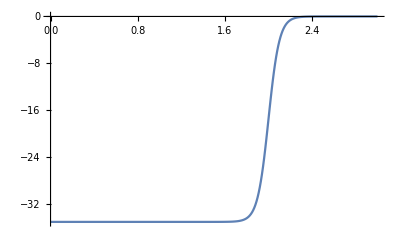

```mathematica
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*calculate Hamiltonian matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[n,-1]-2 one[n,0]+one[n,1]);
```

```mathematica
(*{eval,evec}=Eigensystem[H0];
Manipulate[ListPlot[{rlist,evec⟦-i⟧}ᵀ,Joined->True,PlotRange->All],{i,1,n,1}]*)
```

```mathematica
k[En_]:=Sqrt[-(2μ En)/ℏc^2];
B[En_]:=1-dr k[En];
Hnew[En_]:=Module[{H},H=H0;H[[n,n]]=Vmat[[n,n]]+-ℏc^2/(2 μ) 1/dr^2(-2+B[En]);H]
eigenv[En_,i_]:=({eval,evec}=Eigensystem[Hnew[En]];eval[[-i]])
```

```mathematica
eigenv[-V0/2,1]
```

-8.57826

```mathematica
eval[[-1]]
```

-8.57826

```mathematica
eigenv[-9.2,1]
```

-9.20892

```mathematica
eigenv[%,1]
```

-9.20801

```mathematica
eigenv[%,1]
```

-9.2081

```mathematica
eigenv[%,1]
```

-9.20809

```mathematica
eigenv[%,1]
```

-9.20809

```mathematica
eigenv[%,1]
```

-9.20809

```mathematica
FindRoot[eigenv[En,1]==En,{En,-9.20809,-11,-9}]
```

$Aborted

```mathematica
(*En=-V0;En1=1;*)
```

```mathematica
(*While[Abs[En/En1]≥1.0001||Abs[En/En1]≤0.9999,H=H0;H[[n,n]]=Vmat[[n,n]]+-ℏc^2/(2 μ) 1/dr^2(-2+B[En]);{eval,evec}=Eigensystem[H];En1=En;En=eval[[-1]];]*)
```

```mathematica
En
```

-9.20811

```mathematica
wave[En_,r_]:=Exp[-k[En] r]
```

```mathematica
const[i_]:=evec[[-i,-1]]/wave[eval[[-i]],rmax]
```

```mathematica
Manipulate[ListLinePlot[{Transpose[{rlist,Abs[evec⟦-i⟧]}],Transpose[{Range[rmax,10,dr],const[i] Abs[wave[eval[[-i]],Range[rmax,10,dr]]]}]},PlotRange->All],{i,1,n,1}]
```